```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/error_convolution/4MOST

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenRead[fnamePosIn];
vStream=OpenRead[fnameVelIn];
n0=Read[pStream,Number]
Dimensions[truePositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[trueVelocities=ReadList[vStream,{Number,Number,Number}]]
Close[pStream];
Close[vStream];
```

5000

{5000,3}

{5000,3}

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

5000

5000

{5000,3}

{5000,3}

{5000,6}

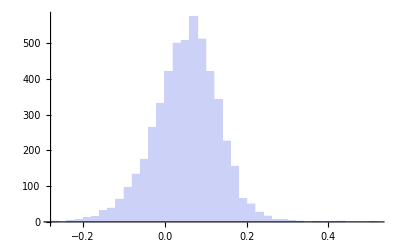

```mathematica
Histogram[convObs[[All,3]]]
```

```mathematica
Tally[posParSel=Thread[convObs[[All,3]]>0.04]]
```

{{True,2915},{False,2085}}

```mathematica
Dimensions[cpSel=Pick[convPositions,posParSel]]
```

{2915,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,posParSel]]
```

{2915,3}

```mathematica
Dimensions[tpSel=Pick[truePositions,posParSel]]
```

{2915,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,posParSel]]
```

{2915,3}

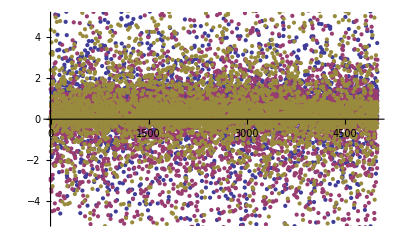

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

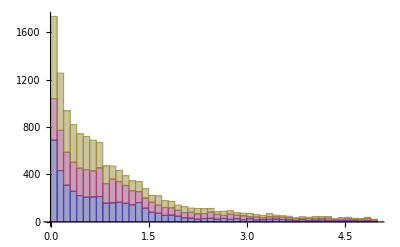

```mathematica
Histogram[Transpose[Abs[(trueVelocities-convVelocities)/trueVelocities]],{0,5,.1},ChartLayout->"Stacked"]
```

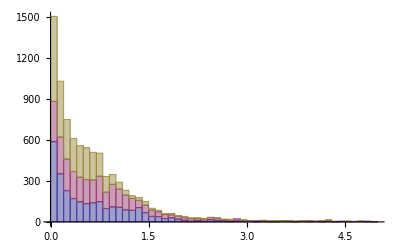

```mathematica
Histogram[Transpose[Abs[(tvSel-cvSel)/tvSel]],{0,5,.1},ChartLayout->"Stacked"]
```